```mathematica
Off[Divide::indet];
SetDirectory[NotebookDirectory[]]
```

/Users/master/Desktop/stereoscope

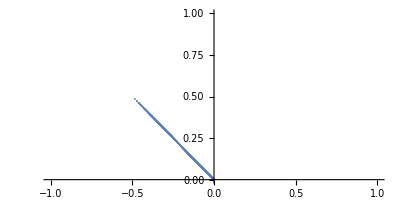

```mathematica
audio=SpeechSynthesize["prova di stereoscope","Luca"];
audioS=AudioPan[audio,-0.999];
coppieLR=Transpose@AudioData[audioS];
fase=(ArcTan[Divide@@#]&/@coppieLR)/.Indeterminate->0;
mag=Sqrt@(#[[1]]^2+#[[2]]^2)&/@coppieLR;
coppieFM=Transpose@{fase+45°,mag};
ListPolarPlot[coppieFM,PlotRange->{{-1,1},{0,1}}]
```

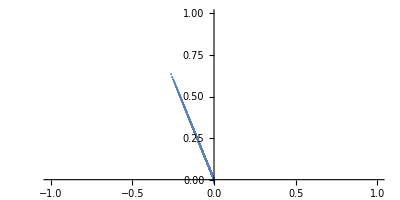

```mathematica
audio=SpeechSynthesize["prova di stereoscope","Luca"];
audioS=AudioPan[audio,-0.5];
coppieLR=Transpose@AudioData[audioS];
fase=(ArcTan[Divide@@#]&/@coppieLR)/.Indeterminate->0;
mag=Sqrt@(#[[1]]^2+#[[2]]^2)&/@coppieLR;
coppieFM=Transpose@{fase+45°,mag};
ListPolarPlot[coppieFM,PlotRange->{{-1,1},{0,1}}]
```

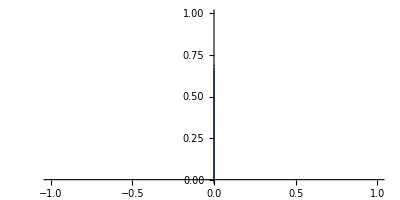

```mathematica
audio=SpeechSynthesize["prova di stereoscope","Luca"];
audioS=AudioPan[audio,0];
coppieLR=Transpose@AudioData[audioS];
fase=(ArcTan[Divide@@#]&/@coppieLR)/.Indeterminate->0;
mag=Sqrt@(#[[1]]^2+#[[2]]^2)&/@coppieLR;
coppieFM=Transpose@{fase+45°,mag};
ListPolarPlot[coppieFM,PlotRange->{{-1,1},{0,1}}]
```

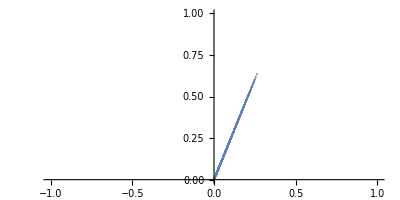

```mathematica
audio=SpeechSynthesize["prova di stereoscope","Luca"];
audioS=AudioPan[audio,0.5];
coppieLR=Transpose@AudioData[audioS];
fase=(ArcTan[Divide@@#]&/@coppieLR)/.Indeterminate->0;
mag=Sqrt@(#[[1]]^2+#[[2]]^2)&/@coppieLR;
coppieFM=Transpose@{fase+45°,mag};
ListPolarPlot[coppieFM,PlotRange->{{-1,1},{0,1}}]
```

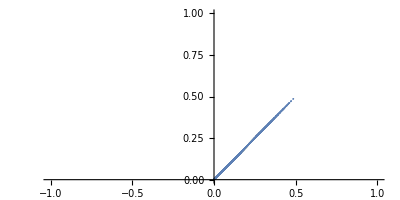

```mathematica
audio=SpeechSynthesize["prova di stereoscope","Luca"];
audioS=AudioPan[audio,0.999];
coppieLR=Transpose@AudioData[audioS];
fase=(ArcTan[Divide@@#]&/@coppieLR)/.Indeterminate->0;
mag=Sqrt@(#[[1]]^2+#[[2]]^2)&/@coppieLR;
coppieFM=Transpose@{fase+45°,mag};
ListPolarPlot[coppieFM,PlotRange->{{-1,1},{0,1}}]
```

```mathematica
audioS=Import["sample1.wav"];
coppieLR=Transpose@AudioData[audioS];
fase=(ArcTan[Divide@@#]&/@coppieLR)/.Indeterminate->0;
mag=Sqrt@(#[[1]]^2+#[[2]]^2)&/@coppieLR;
coppieFM=Transpose@{fase+45°,mag};
Manipulate[
ListPolarPlot[Partition[coppieFM,100,1][[i]],PlotRange->{{-0.5,0.5},{0,0.5}},
PlotStyle->{Black,PointSize[0.005]}
],
{i,1,(Length@coppieFM)-100,1}]
```